## Chapter 0: Functions and exports

```mathematica
Needs["CoolTools`"]
Needs["Carlos`"]
Needs["Quantum`"]
Needs["ThesisTools`"]
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

```mathematica
PNGSetToGif[set_,name_]:=Export["../figures/"<>name<>".gif",
Flatten[{set, Table[set[[i]], {i, Length[set]}]}]];
tickFormat[xmin_,xmax_,digits_,divisions_:10]:=
Function[tickNumber,
{tickNumber,
PaddedForm[Round[tickNumber,0.01],{Max@(Length@IntegerDigits@IntegerPart[#]&/@(10^digits {xmin,xmax})),
digits}]}
]/@FindDivisions[{xmin,xmax},divisions];
```

## Chapter 3: MaxEntAss and its evolution

```mathematica
(*This graphs the radius of the effective state as a function of the Lagrange multiplier*)
Fontsize=18;
RLambda=Plot[
	Evaluate[
		Map[(RadiusAsFunctionOfLagrange[λ,{p,1-p}]/.{p->#})&,{0.1,0.2,0.3,0.5}]],
	{λ,0,8},
	PlotStyle->{{Thickness[0.003],Black},{Thickness[0.003],Red},{Thickness[0.003],Blue},{Thickness[0.003],Darker[Green]}},
	PlotTheme->"FrameGrid",
PlotRange->All,
	FrameLabel->(MaTeX[#,FontSize->Fontsize]&)/@{"\\lambda","r_{\\text{ef}}"},
FrameStyle->Black,
LabelStyle->{FontFamily->"Latin Modern Roman",Black,FontSize->Fontsize-5},
	PlotLegends->Placed[(MaTeX[#,FontSize->Fontsize]&)/@Map["p="<>ToString[#]&,{0.1,0.2,0.3,0.5}],{0.8,0.45}]];
```

## Chapter 4: Effective Dynamics

## 4.1 Local evolutions

```mathematica
(*Parameters: number of particles, probability vector, frecuencies*)
NumberOfParticles =5;
p1 = 0.5;
pk = (1-p1)/(NumberOfParticles-1);
pBoltz=Table[1/NumberOfParticles,NumberOfParticles];
pPref= Join[{p1}, Table[pk,NumberOfParticles-1]];
ωallnorm = RandomVariate[NormalDistribution[μ=2*Pi, σ=0.5], NumberOfParticles];ωallnorm[[1]]=2*Pi;
ωallunif= RandomVariate[UniformDistribution[{a=1,b=3}],NumberOfParticles];ωallunif[[1]]=1.5;
ωprefinveq=Table[2*Pi,NumberOfParticles];ωprefinveq[[1]]=0;
ωprefinran=RandomVariate[UniformDistribution[{a=-3,b=3}],NumberOfParticles];ωprefinran[[1]]=0;
ωnpinv=0;
```

```mathematica
(*Initial effective state*)
ω=ωallunif;
ρef = (IdentityMatrix[2] + (rp=0.9)* ({x,y,z}=Normalize[{1., 1., 0.1}]).Rest[NQubitBasis[1]])/2;
ref = densityMatrixToPoint[{ρef}, NQubitBasis[1]];
```

```mathematica
(*Dynamics functions*)
u[k_, t_, om_]:= MatrixExp[-I t om[[k]] *PauliMatrix[3]];
Γ[rho_, omegas_, p_, t_]:=  
With[{n = Length[omegas], σ = PauliMatrix[3], ρjs = MaxEntSubStates[rho, p]}, 
	 Sum[p[[j]] (u[j,t,omegas].ρjs[[j]].Dagger[u[j,t,omegas]]), {j,n}] ];
BVEvolution[init_, ω_, p_, t_]:= densityMatrixToPoint[{Γ[init, ω, p, t]}, NQubitBasis[1]][[1]];
```

```mathematica
(*Bloch vector function*)
BVt[t_] = BVEvolution[ρef,ω,pPref,t];
```

```mathematica
BVTraj=Show[ParametricPlot[BVt[t][[1;;2]],
{t,tini=0,tend=50},
PlotTheme->"FrameGrid",
	FrameLabel->(MaTeX[#,FontSize->Fontsize]&)/@{"r_{x}","r_{y}"},
PlotStyle->{Thickness[0.003],Black},
FrameStyle->Black,
PlotRange->All,
AspectRatio->Automatic,
	LabelStyle->{FontFamily->"Latin Modern Roman",Black,FontSize->Fontsize-5},
PlotLabel->(MaTeX[#,FontSize->Fontsize]&["p_{1}="<>ToString[p1]<>", n="<>ToString[NumberOfParticles]]),
Epilog->{Darker[Green],PointSize[0.02],Point[BVt[tini][[1;;2]]]}],
ParametricPlot[RotationTransform[4*Pi*t,{0,0,1}][BVt[tini]][[1;;2]],{t,tini=0,tend=0.5},
PlotStyle->{Thickness[0.003],Darker[Blue]}]]
```

```mathematica
label="local_all_ran"<>"_p="<>ToString[p1]<>"_r="<>ToString[rp]<>"_n="<>ToString[NumberOfParticles]<>"_a="<>ToString[a]<>"_b="<>ToString[b];
Export["../notes/thesis/chapter3/figures_separable/"<>label<>".png",BVTraj]
```

../notes/thesis/chapter3/figures_separable/local_all_ran_p=0.5_r=0.9_n=5_a=-3_b=3.png

## 4.2 Quantum gates

### SWAP gate

```mathematica
Fontsize=18;
KLambdaPlot=Plot[
	Evaluate[
		Map[(SWAPContractionFactor[1,p,λ]/.{p->#})&,{0.1,0.2,0.3,0.5}]],
	{λ,0,20},
	PlotStyle->{{Thickness[0.003],Black},{Thickness[0.003],Red},{Thickness[0.003],Blue},{Thickness[0.003],Darker[Green]}},
	PlotTheme->"FrameGrid",
	FrameLabel->(MaTeX[#,FontSize->Fontsize]&)/@{"\\lambda","\\kappa_{1}^{\\rho_{\\text{ef}}}"},
FrameStyle->Black,
LabelStyle->{FontFamily->"Latin Modern Roman",Black,FontSize->Fontsize-5},
	PlotLegends->Placed[(MaTeX[#,FontSize->Fontsize]&)/@Map["p="<>ToString[#]&,{0.1,0.2,0.3,0.5}],{0.8,0.45}]];
KRPlot=Plot[
	Evaluate[
		Map[(SWAPContractionFactor[1,p,LagrangeMulFromRadius[r,{p,1-p}]]/.{p->#})&,{0.1,0.2,0.3,0.5}]],
	{r,0,0.99},
	PlotStyle->{{Thickness[0.003],Black},{Thickness[0.003],Red},{Thickness[0.003],Blue},{Thickness[0.003],Darker[Green]}},
	PlotTheme->"FrameGrid",
	FrameLabel->(MaTeX[#,FontSize->Fontsize]&)/@{"r_{\\text{ef}}","\\kappa_{1}^{\\rho_{\\text{ef}}}"},
FrameStyle->Black,
LabelStyle->{FontFamily->"Latin Modern Roman",Black,FontSize->Fontsize-5}];
```

### CNOT gate

## 4.3 Special Dynamics

### Pauli Channels

### Ising Model

## Appendix: Average Assignment

```mathematica
Export["../figures/ContractionFactorSWAP_2D_lambda0to20.png",swapplot];
```

## Analytical

## CNOT Dynamics

```mathematica
CxHam=Pi*(IdentityMatrix[4]-DirProd[PauliMatrix[3],IdentityMatrix[2]]-DirProd[IdentityMatrix[2],PauliMatrix[3]]+DirProd[PauliMatrix[3],PauliMatrix[1]])/4;
(*Reconstrucción del MaxEnt*)
vec={x,y,z};
rhoA=(IdentityMatrix[2]+Tanh[pλ]*vec.Rest[gellMannBasis[1]]/r)/2;
rhoB=(IdentityMatrix[2]+Tanh[(1-p)λ]*vec.Rest[gellMannBasis[1]]/r)/2;
MaxEnt=DirProd[rhoA,rhoB];
Refine[evMaxEnt=CNOT[t].MaxEnt.Dagger[CNOT[t]],{Element[t,Reals]}];
evcoarse=Refine[CGKraus[evMaxEnt,p],{0<p<1}];
```

```mathematica
MatrixExp[-I*Pi*DirProd[PauliMatrix[3],PauliMatrix[1]]*t/4]//MatrixForm
```

(Cos[(π t)/4] | -ⅈ Sin[(π t)/4] | 0 | 0
-ⅈ Sin[(π t)/4] | Cos[(π t)/4] | 0 | 0
0 | 0 | Cos[(π t)/4] | ⅈ Sin[(π t)/4]
0 | 0 | ⅈ Sin[(π t)/4] | Cos[(π t)/4])

```mathematica
densityMatrixToPoint[{%},gellMannBasis[2]][[1]]/(2*Sqrt[2])
```

{0,0,0,0,0,0,0,0,0,0,0,0,(0.-1. ⅈ) Sin[t],0,0}

```mathematica
MatrixExp[I*Pi*DirProd[PauliMatrix[3],PauliMatrix[1]]/4]//MatrixForm
```

(1/(√2) | ⅈ/(√2) | 0 | 0
ⅈ/(√2) | 1/(√2) | 0 | 0
0 | 0 | 1/(√2) | -ⅈ/(√2)
0 | 0 | -ⅈ/(√2) | 1/(√2))

```mathematica
I*DirProd[PauliMatrix[3],PauliMatrix[1]]//MatrixForm
```

(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0)

```mathematica
CNOT[0]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

## My first differential equation

### Some preliminaries, a simple example

```mathematica
Mt[t_]:=(IdentityMatrix[3]+{{Cos[2*t],-Sin[2*t],0},{Sin[2*t],Cos[2*t],0},{0,0,1}})/2; (*La evolucion no diferencial*)
incon=RandomReal[]*Normalize[Table[RandomReal[],3]]; (*Condicion incial aleatoria*)
s=NDSolve[{{x1'[t],x2'[t],x3'[t]}==H3[t].{x1[t],x2[t],x3[t]},x1[0]==incon[[1]],x2[0]==incon[[2]],x3[0]==incon[[3]]},{x1[t],x2[t],x3[t]},{t,0,π/2}]; (*evolucion diferencial*)
Plot[Norm[Mt[t].incon-{x1[t],x2[t],x3[t]}/.s],{t,0,Pi/2},PlotRange->All]
Plot[{M[t].incon,{x1[t],x2[t],x3[t]}/.s},{t,0,Pi/2},PlotRange->All,PlotLegends->Placed[{"M","Dif"},{0.8,0.7}]]
```

```mathematica
Inverse[{{1,0,0},{0,(1+Exp[-I*t])/2,0},{0,0,1}}]
```

{{1,0,0},{0,1/(1/2+ⅇ^(-ⅈ t)/2),0},{0,0,1}}

```mathematica
(*Vectorizing and devectorizing functions*)
VectorizeDO[do_]:=Flatten[do];
Devectorized[do_,shape_]:=ArrayReshape[do,shape];
shape1={2,2};
shape2={4,4};

(*Unitary, hamiltonian, rho(t), and superoperator*)
Ut=KroneckerProduct[IdentityMatrix[2],MatrixExp[-I*PauliMatrix[3]]];
Ham=KroneckerProduct[IdentityMatrix[2],PauliMatrix[3]];
rhot={{r00,r01},{r10,r11}};
Gt={{1,0,0,0},
{0,(1+Exp[-I*t])/2,0,0},
{0,0,(1+Exp[I*t])/2,0},
{0,0,0,1}};
Gtinv=Inverse[Gt]//FullSimplify;

(*Assignement map*)
Assign[do_]:=KroneckerProduct[do,do];

(*First, apply inverse dynamics to vectorized density operator, then get assmap*)
asst=Assign[Devectorized[Gtinv.VectorizeDO[rhot],shape1]]//FullSimplify;
(*Evolve the result using the unitary dynamics*)
evass=Ut.asst.Dagger[Ut]//FullSimplify;
(*Calculate the commutator with the hamiltonian*)
conm=Commutator[Ham,evass]//FullSimplify;
(*Take the CG*)
dev=(CGKraus[conm,1/2]//FullSimplify)/.(r00+r11->1);
VectorizeDO[dev]//MatrixForm
```

(0
(2 ⅇ^(-2 ⅈ) r01)/(1+ⅇ^(-ⅈ t))
-(2 ⅇ^(2 ⅈ) r10)/(1+ⅇ^(ⅈ t))
0)

```mathematica
TM={{1,0,0,1},{0,1,-I,0},{0,1,I,0},{1,0,0,-1}}/2;
MT=Inverse[TM];
rhop={1,x,y,z}
Devectorized[TM.rhop,shape1]//MatrixForm;
HP={{0,0,0,0},{0,-Tan[t],-1,0},{0,1,-Tan[t],0},{0,0,0,0}};
TM.HP.MT//FullSimplify
```

{1,x,y,z}

{{0,0,0,0},{0,-ⅈ-Tan[t],0,0},{0,0,ⅈ-Tan[t],0},{0,0,0,0}}

### Another example, an equation for the microscopic SWAP

```mathematica
H=I*MatrixLog[SWAP[1]]
```

{{0,0,0,0},{0,-π/2,π/2,0},{0,π/2,-π/2,0},{0,0,0,0}}

```mathematica
(*Vectorizing and devectorizing functions*)
VectorizeDO[do_]:=Flatten[do];
Devectorized[do_,shape_]:=ArrayReshape[do,shape];
shape1={2,2};
shape2={4,4};

(*Unitary, hamiltonian, rho(t), and superoperator*)
Ut=SWAP[t];
Ham=H;
rhot={{r00,r01},{r10,r11}};
Gt={{1,0,0,0},
{0,(1+Exp[-I*t])/2,0,0},
{0,0,(1+Exp[I*t])/2,0},
{0,0,0,1}};
Gtinv=Inverse[Gt]//FullSimplify;

(*Assignement map*)
Assign[do_]:=KroneckerProduct[do,do];

(*First, apply inverse dynamics to vectorized density operator, then get assmap*)
asst=Assign[Devectorized[Gtinv.VectorizeDO[rhot],shape1]]//FullSimplify;
(*Evolve the result using the unitary dynamics*)
evass=Ut.asst.Dagger[Ut]//FullSimplify;
(*Calculate the commutator with the hamiltonian*)
conm=Commutator[Ham,evass]//FullSimplify;
(*Take the CG*)
dev=(CGKraus[conm,1/2]//FullSimplify)/.(r00+r11->1);
VectorizeDO[dev]//MatrixForm
```

```mathematica
BoltzmannClone[rho_]:=KroneckerProduct[rho,rho];
rho={{r00,r01},{r10,r11}};
ev=Refine[SWAP[t].BoltzmannClone[rho].Dagger[SWAP[t]],{Element[t,Reals]}]//FullSimplify;
ev==BoltzmannClone[rhot]
```

True

```mathematica
SWAP[t]//MatrixForm
```

(1 | 0 | 0 | 0
0 | ⅇ^((ⅈ π t)/2) Cos[(π t)/2] | -ⅈ ⅇ^((ⅈ π t)/2) Sin[(π t)/2] | 0
0 | -ⅈ ⅇ^((ⅈ π t)/2) Sin[(π t)/2] | ⅇ^((ⅈ π t)/2) Cos[(π t)/2] | 0
0 | 0 | 0 | 1)

```mathematica
Refine[SWAP[t].BoltzmannClone[rhot].Dagger[SWAP[t]],{Element[t,Reals]}]
```

```mathematica
Depolarizing[rho_,lam_]:=(1-lam)*IdentityMatrix[2]/2+lam*rho;
rho={{r00,r01},{r10,r11}};
Depolarizing[Depolarizing[rho,1/λ],λ]//FullSimplify
```

{{r00,r01},{r10,r11}}

```mathematica
I*MatrixExp[-I*PauliMatrix[3]*Pi/2]
```

{{1,0},{0,-1}}

{{λ_3,λ_1-ⅈ λ_2},{λ_1+ⅈ λ_2,-λ_3}}

```mathematica
MaxEnt[rhovec_,p_]:=With[{vecA=MapAt[#*p*Tanh[p*λ]/r&,rhovec,{{2},{3},{4}}],vecB=MapAt[#*(1-p)*Tanh[(1-p)*λ]/r&,rhovec,{{2},{3},{4}}]},Flatten[KroneckerProduct[vecA,vecB]]];
vec={1,x,y,z};
inv[vec_,κ_]:=MapAt[#/κ&,vec,{{2},{3},{4}}]

inv[vec,κ]
psi0vec=MaxEnt[inv[vec,κ],p];
psi0=psi0vec.gellMannBasis[2]/2//FullSimplify;
```

{1,x/κ,y/κ,z/κ}

```mathematica
psit=Refine[SWAP[t].psi0.Dagger[SWAP[t]],{Element[t,Reals],Element[p,Reals]}]//FullSimplify;
```

```mathematica
conm=Commutator[I*MatrixLog[SWAP[1]],psit];
dev=CGKraus[conm,p]//FullSimplify;
```

```mathematica
change=Refine[densityMatrixToPoint[{dev},gellMannBasis[1]],{Element[t,Reals],Element[p,Reals]}][[1]]//FullSimplify;
```

```mathematica
Refine[change,{0<p<1}]//FullSimplify//MatrixForm
```

(((-0.5+1. p) ((0.-4.44288 ⅈ) p r κ (z Cos[π t]-1. x Sin[π t]) Tanh[p λ]-(0.+4.44288 ⅈ) (-1.+1. p) (-1. r x κ Sin[π t]+1. p y z Cos[π t] Tanh[p λ]) Tanh[λ-p λ]))/(r^2 κ^2)
((0.+4.44288 ⅈ) ((0.5+p (-1.5+1. p)) r y κ Sin[π t]+p x (((-0.5+(1.5-1. p) p) y+(0.5+p (-1.5+1. p)) z) Cos[π t]+(-0.5+(1.5-1. p) p) x Sin[π t]) Tanh[p λ]) Tanh[λ-p λ])/(r^2 κ^2)
(((0.+4.44288 ⅈ)+((0.-13.3286 ⅈ)+(0.+8.88577 ⅈ) p) p) r z κ Cos[(π t)/2] Sin[(π t)/2] Tanh[λ-p λ]+p y Tanh[p λ] (((0.+2.22144 ⅈ)-(0.+4.44288 ⅈ) p) r κ Cos[π t]-(0.+4.44288 ⅈ) (0.5+p (-1.5+1. p)) (y Cos[π t]+x Sin[π t]) Tanh[λ-p λ]))/(r^2 κ^2))

Missing[UnknownSymbol,Product`]

```mathematica
densityMatrixToPoint[{SWAP[1]},gellMannBasis[2]][[1]]
```

{0,0,0,0,0,0,1.41421,0,0,0,1.41421,0,0,0,1.41421}

```mathematica
Sum[LeviCivitaTensor[3][[i,j,3]],{i,3},{j,3}]
```

0

```mathematica
sumsigma=Sum[KroneckerProduct[PauliMatrix[i],PauliMatrix[i]],{i,3}]/2
```

{{1/2,0,0,0},{0,-1/2,1,0},{0,1,-1/2,0},{0,0,0,1/2}}

```mathematica
rep[mat_]:=densityMatrixToPoint[{mat},gellMannBasis[2]][[1]]/(2*Sqrt[2.])
dotpower[mat_,n_]:=Nest[#.mat&,mat,n]
```

```mathematica
dotpower[sumsigma,1]
```

{{1/4,0,0,0},{0,5/4,-1,0},{0,-1,5/4,0},{0,0,0,1/4}}

```mathematica
rep[sumsigma.sumsigma.sumsigma.sumsigma]
```

{0.,0.,0.,0.,0.,0.,-1.25,0.,0.,0.,-1.25,0.,0.,0.,-1.25}

{{0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,1.,0.,0.,0.,1.}}

```mathematica
2*Sqrt[2.]
```

2.82843

```mathematica
SWAP[t]//MatrixForm
```

(1 | 0 | 0 | 0
0 | ⅇ^((ⅈ π t)/2) Cos[(π t)/2] | -ⅈ ⅇ^((ⅈ π t)/2) Sin[(π t)/2] | 0
0 | -ⅈ ⅇ^((ⅈ π t)/2) Sin[(π t)/2] | ⅇ^((ⅈ π t)/2) Cos[(π t)/2] | 0
0 | 0 | 0 | 1)

```mathematica
densityMatrixToPoint[{SWAP[t]},gellMannBasis[2]][[1]]//MatrixForm
```

(0
0
0
0
0
0
(0.-1.41421 ⅈ) ⅇ^((ⅈ π t)/2) Sin[(π t)/2]
0
0
0
(0.-1.41421 ⅈ) ⅇ^((ⅈ π t)/2) Sin[(π t)/2]
0
0
0
1.41421-1.41421 ⅇ^((ⅈ π t)/2) Cos[(π t)/2])

```mathematica
I*densityMatrixToPoint[{MatrixLog[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}}]},gellMannBasis[2]]
```

{{0,0,2.22144+0. ⅈ,0,0,2.22144+0. ⅈ,0,0,0,0,0,0,0,0,-2.22144+0. ⅈ}}

```mathematica
H={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1}};
U[t_]:=MatrixExp[-I*t*H];
rho={{r00,r01},{r10,r11}};;
psi=KroneckerProduct[rho,rho];
psit=Refine[U[t].psi.Dagger[U[t]],{Element[t,Reals]}];
rhot=CGKraus[psit,1/2]//FullSimplify//MatrixForm
```

(r00 (r00+r11) | r01 (r00+ⅇ^(ⅈ t) r11)
r10 (r00+ⅇ^(-ⅈ t) r11) | r11 (r00+r11))

```mathematica
densityMatrixToPoint[{rhot},gellMannBasis[1]][[1]]//FullSimplify//MatrixForm
```

(1/2 (x (1+z)-x (-1+z) Cos[t]-y (-1+z) Sin[t])
1/2 (y (1+z)-y (-1+z) Cos[t]+x (-1+z) Sin[t])
z)

```mathematica
OBTAIN IMAGE OF THE EVOLUTION
```

```mathematica
Inverse[(IdentityMatrix[3]*(1+z)+-(z-1)*{{Cos[t],-Sin[t],0},{Sin[t],Cos[t],0},{0,0,1}})/2]//FullSimplify//MatrixForm
```

(1/(1+z-(2 z)/(1+z+Cos[t]-z Cos[t])) | -((-1+z) Sin[t])/(1+z^2+Cos[t]-z^2 Cos[t]) | 0
((-1+z) Sin[t])/(1+z^2+Cos[t]-z^2 Cos[t]) | 1/(1+z-(2 z)/(1+z+Cos[t]-z Cos[t])) | 0
0 | 0 | 1)

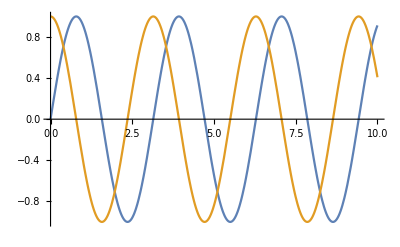

```mathematica
Plot[{Sin[2x],Cos[x]^2-Sin[x]^2},{x,0,10}]
```